```mathematica
mdwout = "/Volumes/homes/Code/cytomod/shila/semiflexible/out/network/";
mdwlcl="/home/simonfreedman/scratch-midway/cytomod/out/pl/";
mdwhm="/home/simonfreedman/Code/cytomod/shila/semiflexible/out/pl/";
```

```mathematica
ParticleTimeSeries[d_,n_]:=
Module[
{dir=d, name=n},
file=dir<>"/txt_stack/"<>name<>".txt";
particles=Import[file,"Table"];
(*Print["Finished importing "<>file];*)
timestamps = Position[particles,"t"][[All,1]];
particlesT=Table[particles[[timestamps[[i]]+1;;timestamps[[i+1]]-1]],{i,Length[timestamps]-1}];
particlesT=Append[particlesT, particles[[timestamps[[-1]]+1;;]]];
nparticles=Length[particlesT[[1]]];
dt=particles[[timestamps[[2]],3]]-particles[[timestamps[[1]],3]];
{nparticles, dt,particlesT}
];
```

```mathematica
CCF[d_,decorframe_]:=
Module[
{dir =d,
ndc=decorframe},
{np, dt,rt}=ParticleTimeSeries[d,"rods"];
{np,dt,lt}=ParticleTimeSeries[d,"links"];
nlinksT=Table[Length[l],{l,lt}];
fracture=Position[nlinksT,Except[Head[nlinksT]|nlinksT[[1]]],1,1];
fractureT=If[Length[fracture]>0, fracture[[1,1]],Length[rt]];
rt=rt[[1;;fractureT]];
anglesT=ArcTan[rt[[All,All,3]],rt[[All,All,4]]];
ld=Sqrt[rt[[1,1,3]]^2+rt[[1,1,4]]^2];
firstRod=Ceiling[Length[rt[[1]]]/4];
lastRod=Floor[Length[rt[[1]]]*3/4];
corrs=Table[{(j-i)*ld,
Cos[anglesT[[t,j]]-anglesT[[t,i]]]},{t,Ceiling[Length[rt]/2],Length[rt],ndc},
{i,firstRod,lastRod},
{j,i,lastRod}];
gatheredCoors = Gather[Flatten[corrs,2],First[#1]==First[#2]&];
ccf=Table[Mean[gc],{gc,gatheredCoors}];
errs=Table[StandardDeviation[gatheredCoors[[i,All,2]]]/Sqrt[Length[gatheredCoors[[i]]]],{i,Length[gatheredCoors]}];
{ccf,errs}
];
```

```mathematica
seeds=Table[ToString[i],{i,3101,3200}];
basedir="nm200_seed";
dirs=Table[mdwlcl<>basedir<>s,{s,seeds}];
```

```mathematica
lowKaps={".04",".08",".12",".16",".20",".24",".28",".32",".36",".40",".44",".48",".52",".56",".60",".64",".68",".72",".76",".80",".84",".88",".92",".96","1.00","1.04","1.08","1.12","1.16","1.20","1.24","1.28","1.32","1.36","1.40","1.44","1.48","1.52","1.56","1.60","1.64","1.68","1.72","1.76","1.80","1.84","1.88","1.92"};
higherKaps={".5","1.0","1.5","2.0","2.5","3.0","3.5","4.0","4.5","5.0","5.5","6.0","6.5","7.0","7.5","8.0","8.5","9.0","9.5","10.0","10.5","11.0","11.5","12.0","12.5","13.0","13.5","14.0","14.5","15.0","15.5","16.0","16.5","17.0","17.5","18.0","18.5","19.0","19.5","20.0","20.5","21.0","21.5","22.0","22.5","23.0","23.5","24.0"};
kaps={"30","50","70","90","110","130","150","170","190"};
basedir="nm50_linear_bend_kapb";
dirs=Table[mdwlcl<>basedir<>s,{s,kaps}];
```

```mathematica
kaps={".001",".002",".003",".004",".005",".006",".007",".008",".009",
".010",".020",".030",".040",".050",".060",".070",".080",".090",
".100",".200",".300",".400",".500",".600",".700",".800",".900",
"1.000","2.000","3.000","4.000","5.000","6.000","7.000","8.000","9.000","10.000"};
basedir="nm200_kapb";
dirs=Table[mdwlcl<>basedir<>s,{s,kaps}];
```

```mathematica
kT=.004;
```

```mathematica
ccfs=Table[CCF[dr,10],{dr,dirs[[1;;10]]}];
```

```mathematica
ccfsBar=ccfs;
```

```mathematica
ccfsBar=Table[{MovingAverage[ccfs[[i,1]],10],MovingAverage[ccfs[[i,2]],2]},{i,Length[ccfs]}];
```

```mathematica
ccfsBar=Table[{Mean[Partition[ccfs[[i,1]],20]],Mean[Partition[ccfs[[i,2]],20]}
```

```mathematica
nlms=Table[
NonlinearModelFit[
ccfsBar[[i,1,2;;]],
Exp[-x/(2*Lp)],
{{Lp,.04/kT}},
x,
Weights->1/ccfsBar[[i,2]]^2
],
{i,Length[ccfsBar]}];
```

Part::partd: Part specification kaps ⟦ 1 ⟧ is longer than depth of object.

ToExpression::notstrbox: kaps ⟦ 1 ⟧ is not a string or a box. ToExpression can only interpret strings or boxes as Mathematica input.

NonlinearModelFit::srect: Value 250.\ $Failed in search specification {Lp, 250.\ $Failed} is not a number or array of numbers.

Part::partd: Part specification kaps ⟦ 2 ⟧ is longer than depth of object.

ToExpression::notstrbox: kaps ⟦ 2 ⟧ is not a string or a box. ToExpression can only interpret strings or boxes as Mathematica input.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

NonlinearModelFit::wts: The value of option Weights -> {ComplexInfinity, ComplexInfinity, ComplexInfinity, ComplexInfinity, ComplexInfinity, ComplexInfinity, ComplexInfinity, ComplexInfinity, ComplexInfinity, « 33 », ComplexInfinity, ComplexInfinity, ComplexInfinity, ComplexInfinity, ComplexInfinity, ComplexInfinity, ComplexInfinity, ComplexInfinity, « 50 »} should be a list of real numbers or a pure function.

Part::partd: Part specification kaps ⟦ 3 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

ToExpression::notstrbox: kaps ⟦ 3 ⟧ is not a string or a box. ToExpression can only interpret strings or boxes as Mathematica input.

General::stop: Further output of ToExpression :: notstrbox will be suppressed during this calculation.

NonlinearModelFit::srect: Value 250.\ $Failed in search specification {Lp, 250.\ $Failed} is not a number or array of numbers.

General::stop: Further output of NonlinearModelFit :: srect will be suppressed during this calculation.

NonlinearModelFit::wts: The value of option Weights -> {ComplexInfinity, ComplexInfinity, ComplexInfinity, ComplexInfinity, ComplexInfinity, ComplexInfinity, ComplexInfinity, ComplexInfinity, ComplexInfinity, « 33 », ComplexInfinity, ComplexInfinity, ComplexInfinity, ComplexInfinity, ComplexInfinity, ComplexInfinity, ComplexInfinity, ComplexInfinity, « 50 »} should be a list of real numbers or a pure function.

General::stop: Further output of NonlinearModelFit :: wts will be suppressed during this calculation.

Part::partd: Part specification kaps ⟦ 1 ⟧ is longer than depth of object.

NonlinearModelFit::srect: Value 250.\ $Failed in search specification {Lp, 250.\ $Failed} is not a number or array of numbers.

NonlinearModelFit::wts: The value of option Weights -> {ComplexInfinity, ComplexInfinity, ComplexInfinity, ComplexInfinity, ComplexInfinity, ComplexInfinity, ComplexInfinity, ComplexInfinity, ComplexInfinity, « 33 », ComplexInfinity, ComplexInfinity, ComplexInfinity, ComplexInfinity, ComplexInfinity, ComplexInfinity, ComplexInfinity, ComplexInfinity, « 50 »} should be a list of real numbers or a pure function.

NonlinearModelFit::srect: Value 250.\ $Failed in search specification {Lp, 250.\ $Failed} is not a number or array of numbers.

General::stop: Further output of NonlinearModelFit :: srect will be suppressed during this calculation.

NonlinearModelFit::wts: The value of option Weights -> {ComplexInfinity, ComplexInfinity, ComplexInfinity, ComplexInfinity, ComplexInfinity, ComplexInfinity, ComplexInfinity, ComplexInfinity, ComplexInfinity, « 33 », ComplexInfinity, ComplexInfinity, ComplexInfinity, ComplexInfinity, ComplexInfinity, ComplexInfinity, ComplexInfinity, ComplexInfinity, « 50 »} should be a list of real numbers or a pure function.

General::stop: Further output of NonlinearModelFit :: wts will be suppressed during this calculation.

Part::partd: Part specification « 1 » ⟦ 1, 1 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

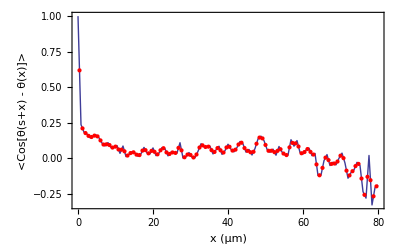
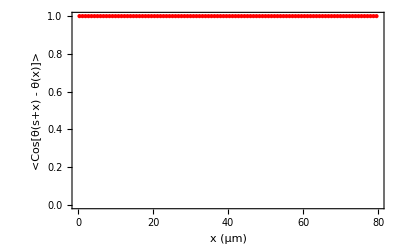
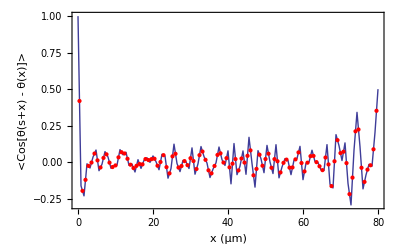
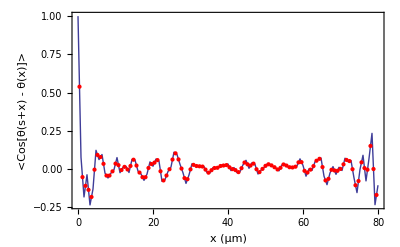
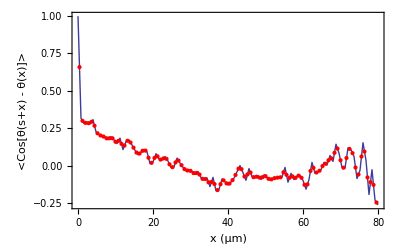
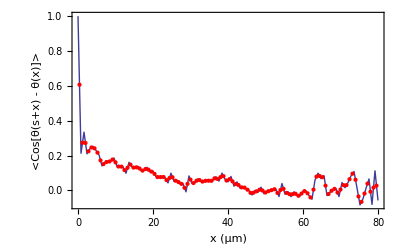
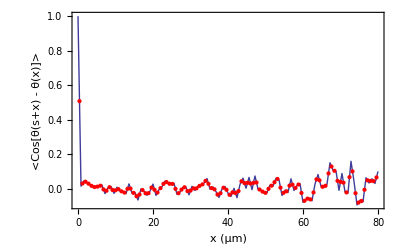
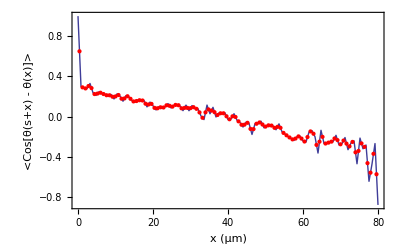
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[
Show[
ListLinePlot[ccfs[[i,1]],Frame->True,
FrameLabel->{
"x (μm)", 
"<Cos[θ(s+x) - θ(x)]>",
"κ_input= "<>ToString[kaps[[i]]]<>"\nκ_measured = "<>ToString[0.004*nlms[[i]]["ParameterTableEntries"][[1,1]]]
},PlotRange->Full
],
ListPlot[ccfsBar[[i,1]],Frame->True,
PlotStyle->{Red},PlotRange->Full
],
Plot[Normal[nlms[[i]]]/.x->l,{l,0,40},PlotRange->Full,PlotStyle->{Black}]
],
{i,Length[ccfs]}]
```

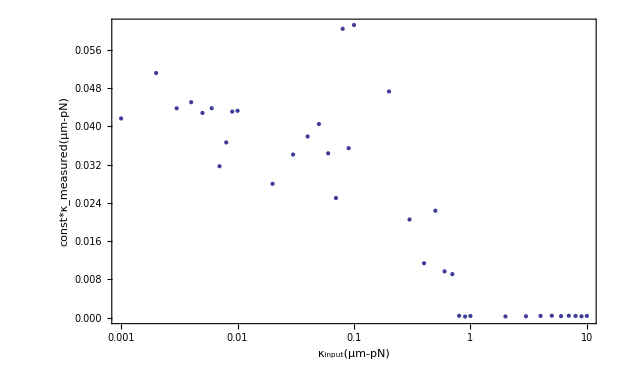

```mathematica
kappakappa=Table[{ToExpression[kaps[[i]]],nlms[[i]]["ParameterTableEntries"][[1,1]]*.004},{i,Length[kaps]}];
ListLogLinearPlot[kappakappa,Frame->True,FrameLabel->{"κ_input(μm-pN)","const*κ_measured(μm-pN)","Linear forcing springs"},PlotRange->Full,BaseStyle->{FontSize->16}]
```

```mathematica
LinearModelFit[kappakappa,x,x]
```

FittedModel[0.0057112+0.000476014 x]

```mathematica
1/.000476
```

2100.84

```mathematica
2100*.04
```

84.

```mathematica
0.4/0.011
```

36.3636

```mathematica
20*0.04
```

0.8

```mathematica
scale
```

416.

```mathematica
Table[{nlms[[i]]["ParameterTable"],seeds[[i]]},{i,Length[nlms]}]//TableForm
```

```mathematica
Histogram[Table[nlms[[i]]["ParameterTableEntries"][[1,1]],{i,Length[nlms]}],100,Frame->True, FrameLabel->{"Lp(um)","counts","Distribution of persistence lengths as measured by CCF"},BaseStyle->{FontSize->16}]
```

```mathematica
pls=Table[nlms[[i]]["ParameterTableEntries"][[1,1]],{i,Length[nlms]}];
```

```mathematica
Mean[pls]
```

64.7173

```mathematica
Min[Table[Length[ccfs[[i,1]]],{i,Length[ccfs]}]]
```

40

```mathematica
meanccfs=Total[ccfs[[All,1,1;;Min[Table[Length[ccfs[[i,1]]],{i,Length[ccfs]}]]]]]/Length[ccfs];
```

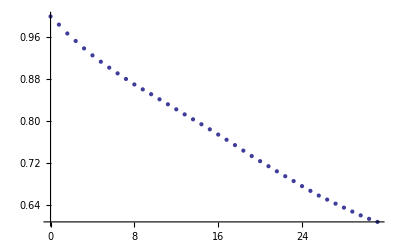

```mathematica
ListPlot[meanccfs]
```

```mathematica
nlm=NonlinearModelFit[
meanccfs,
Exp[-x/(2Lp)],
{Lp},
x];
```

```mathematica
nlm["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
Lp | 30.7481 | 0.123067 | 249.849 | 4.11909×10^-64

```mathematica
Series[Cos[x],{x,0,4}]
```

1-x^2/2+x^4/24+O[x]^5

```mathematica
Series[Sqrt[1-x],{x,0,4}]
```

1-x/2-x^2/8-x^3/16-(5 x^4)/128+O[x]^5

```mathematica
FullSimplify[(1-Cos[θ/2])]
```

2 Sin[θ/4]^2

```mathematica
Series[1-2Cos[x/2]+Cos[x/2]^2,{x,0,6}]
```

x^4/64-x^6/1536+O[x]^7

```mathematica
Cos[π-x]
```

-Cos[x]

```mathematica
FullSimplify[1/2(1+Cos[θ])]
```

Cos[θ/2]^2